```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={ρ[s]>0}
```

{ρ[s]>0}

```mathematica
(*s_here = x_1_notes*)
```

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[s_]:={{ρ'[s]^2+ζ'[s]^2,0},{0,ρ[s]^2}}
```

```mathematica
detg[s]:=Det[g[s]]
```

```mathematica
sqrtdetg[s_]:=Sqrt[detg[s]]
```

```mathematica
ig[s]:=Inverse[g[s]]//FullSimplify
```

```mathematica
ig[s]
```

{{1/(ζ'[s]^2+ρ'[s]^2),0},{0,1/ρ[s]^2}}

```mathematica
eqρ=ρ'[s]-Cos[ψ[s]]
```

-Cos[ψ[s]]+ρ'[s]

```mathematica
eqζ=ζ'[s]+Sin[ψ[s]]
```

Sin[ψ[s]]+ζ'[s]

```mathematica
rep={ρ'[s]->Cos[ψ[s]],ζ'[s]->-Sin[ψ[s]],
ρ''[s]->-Sin[ψ[s]]ψ'[s],ζ''[s]->-Cos[ψ[s]]ψ'[s],
ρ'''[s]->-Cos[ψ[s]] ψ'[s]^2-Sin[ψ[s]] ψ''[s],ζ'''[s]->Sin[ψ[s]] ψ'[s]^2-Cos[ψ[s]] ψ''[s],
ρ''''[s]->-3 Cos[ψ[s]] ψ'[s] ψ''[s]+Sin[ψ[s]] (ψ'[s]^3-Derivative[3][ψ][s]),
ζ''''[s]->3 Sin[ψ[s]] ψ'[s] ψ''[s]+Cos[ψ[s]] (ψ'[s]^3-Derivative[3][ψ][s])};
```

```mathematica
D[-Sin[ψ[s]],{s,3}]//FullSimplify
```

3 Sin[ψ[s]] ψ'[s] ψ''[s]+Cos[ψ[s]] (ψ'[s]^3-ψ^(3)[s])

```mathematica
{ρ'[s]Cos[θ],ρ'[s]Sin[θ],ζ'[s]} /.rep
```

{Cos[θ] Cos[ψ[s]],Cos[ψ[s]] Sin[θ],-Sin[ψ[s]]}

```mathematica
{-ρ[s]Sin[θ],ρ[s]Cos[θ],0}/.rep
```

{-Sin[θ] ρ[s],Cos[θ] ρ[s],0}

```mathematica
e[1][{s_,θ_}]:={Cos[θ] Cos[ψ[s]],Cos[ψ[s]] Sin[θ],-Sin[ψ[s]]}
e[2][{s_,θ_}]:= {-Sin[θ] ρ[s],Cos[θ] ρ[s],0}
```

```mathematica
normal[{s_,θ_}]:=-FullSimplify[Cross[e[1][{s,θ}],e[2][{s,θ}]]/sqrtdetg[s],Assumptions->ass]/.rep
```

```mathematica
normal[{s,θ}]//Simplify
```

{-Cos[θ] Sin[ψ[s]],-Sin[θ] Sin[ψ[s]],-Cos[ψ[s]]}

```mathematica
Derivative[ϵ[1]][e[1]][{s,θ}].normal[{s,θ}]//FullSimplify
```

ψ'[s]

```mathematica
Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

(Sin[ψ[r]] ρ[r]^2)/(√detg[r])

```mathematica
b[s_]:={{Derivative[ϵ[1]][e[1]][{s,θ}].normal[{s,θ}],Derivative[ϵ[1]][e[2]][{s,θ}].normal[{s,θ}]},{Derivative[ϵ[2]][e[1]][{s,θ}].normal[{s,θ}],Derivative[ϵ[2]][e[2]][{s,θ}].normal[{s,θ}]}}//FullSimplify
```

```mathematica
1/2Sum[ig[s][[i,j]]b[s][[i,j]],{i,1,2},{j,1,2}]/.rep//FullSimplify
```

(Sin[ψ[s]]+ρ[s] ψ'[s])/(2 ρ[s])

```mathematica
H[s_]:=(Sin[ψ[s]]+ρ[s] ψ'[s])/(2 ρ[s])
```

```mathematica
H[s]
```

(Sin[ψ[s]]+ρ[s] ψ'[s])/(2 ρ[s])

```mathematica
Γ[s_]:=ResourceFunction["ChristoffelSymbol"][g[s],{ s,θ}]/.rep //FullSimplify//MatrixForm
```

```mathematica
Γ[s]//MatrixForm
```

((0
0) | (0
-Cos[ψ[s]] ρ[s])
(0
Cos[ψ[s]]/ρ[s]) | (Cos[ψ[s]]/ρ[s]
0))

```mathematica
K[s_]:=Det[b[s]]/detg[s]/.rep//FullSimplify
```

```mathematica
K[s]
```

(Sin[ψ[s]] ψ'[s])/ρ[s]

```mathematica
ϕ[s_]:=ig[s][[1,1]]H'[s]/.rep//FullSimplify
```

```mathematica
ϕ'[s]+ig[s][[1,1]]H'[s]Cos[ψ[s]]/ρ[s]/.rep//FullSimplify
```

(Sin[ψ[s]]+Sin[3 ψ[s]]-4 Cos[2 ψ[s]] ρ[s] ψ'[s]+ρ[s]^2 (-4 Sin[ψ[s]] ψ'[s]^2+8 Cos[ψ[s]] ψ''[s])+4 ρ[s]^3 ψ^(3)[s])/(8 ρ[s]^3)

```mathematica
NabNabH[s_]:=ϕ'[s]+ig[s][[1,1]]H'[s]Cos[ψ[s]]/ρ[s]/.rep//FullSimplify
```

```mathematica
eq=2κ (2 H[s](H[s]^2-K[s])+NabNabH[s])-2 σ[s]H[s]/.rep//FullSimplify
```

1/(8 ρ[s]^3)(κ (5 Sin[ψ[s]]+Sin[3 ψ[s]])-2 ρ[s] (κ (1+3 Cos[2 ψ[s]]) ψ'[s]+2 ρ[s] (2 σ[s] (Sin[ψ[s]]+ρ[s] ψ'[s])+κ (3 Sin[ψ[s]] ψ'[s]^2-4 Cos[ψ[s]] ψ''[s]-ρ[s] (ψ'[s]^3+2 ψ^(3)[s])))))

```mathematica
eq//Expand
```

(5 κ Sin[ψ[s]])/(8 ρ[s]^3)+(κ Sin[3 ψ[s]])/(8 ρ[s]^3)-(Sin[ψ[s]] σ[s])/ρ[s]-(κ ψ'[s])/(4 ρ[s]^2)-(3 κ Cos[2 ψ[s]] ψ'[s])/(4 ρ[s]^2)-σ[s] ψ'[s]-(3 κ Sin[ψ[s]] ψ'[s]^2)/(2 ρ[s])+1/2 κ ψ'[s]^3+(2 κ Cos[ψ[s]] ψ''[s])/ρ[s]+κ ψ^(3)[s]

```mathematica
(*the left-hand side of the ODE as in dereny 2002 paper*)
```

```mathematica
eqdereny=-(κ (-Derivative[3][ψ][s]-1/2 (ψ'[s])^3 - 2 Cos[ψ[s]]/ρ[s]ψ''[s]+3 Sin[ψ[s]]/(2 ρ[s]) ψ'[s]^2+(3 Cos[ψ[s]]^2-1)/(2 ρ[s]^2) ψ'[s]
-(Cos[ψ[s]]^2+1)/(2 ρ[s]^3)Sin[ψ[s]]
)+σ[s]/ρ[s]Sin[ψ[s]]+σ[s] ψ'[s])
```

-(Sin[ψ[s]] σ[s])/ρ[s]-σ[s] ψ'[s]-κ (-((1+Cos[ψ[s]]^2) Sin[ψ[s]])/(2 ρ[s]^3)+((-1+3 Cos[ψ[s]]^2) ψ'[s])/(2 ρ[s]^2)+(3 Sin[ψ[s]] ψ'[s]^2)/(2 ρ[s])-1/2 ψ'[s]^3-(2 Cos[ψ[s]] ψ''[s])/ρ[s]-ψ^(3)[s])

```mathematica
(*check: the equations are the same as in dereny's 2002 paper*)
```

```mathematica
eq-eqdereny//FullSimplify
```

0

```mathematica
rep2={ψ[s]->φ[ρ[s]],
ψ'[s]->Cos[ψ[s]] φ'[ρ[s]],
ψ''[s]->-Cos[φ[ρ[s]]] Sin[φ[ρ[s]]] φ'[ρ[s]]^2+Cos[φ[ρ[s]]]^2 φ''[ρ[s]],
ψ'''[s]->Cos[φ[ρ[s]]] (-Cos[2 φ[ρ[s]]] φ'[ρ[s]]^3-2 Sin[2 φ[ρ[s]]] φ'[ρ[s]] φ''[ρ[s]]+Cos[φ[ρ[s]]]^2 Derivative[3][φ][ρ[s]]),
ψ''''[s]->Cos[φ[ρ[s]]] (1/2 (Sin[φ[ρ[s]]]+3 Sin[3 φ[ρ[s]]]) φ'[ρ[s]]^4-1/2 (5 Cos[φ[ρ[s]]]+9 Cos[3 φ[ρ[s]]]) φ'[ρ[s]]^2 φ''[ρ[s]]-7 Cos[φ[ρ[s]]]^2 Sin[φ[ρ[s]]] φ'[ρ[s]] Derivative[3][φ][ρ[s]]+Cos[φ[ρ[s]]]^2 (-4 Sin[φ[ρ[s]]] φ''[ρ[s]]^2+Cos[φ[ρ[s]]] Derivative[4][φ][ρ[s]])),
σ[s]->τ[ρ[s]]};
```

```mathematica
(*D[φ[ρ[s]],{s,4}]/.rep/.rep2/.rep2//FullSimplify*)
```

```mathematica
(*this is the ODE transformed : it depends only on φ (dependent variable) and ρ[s] (independent variable)*)
```

```mathematica
eq/.rep2/.rep2/.{ρ[s]->r}//FullSimplify
```

1/(8 r^3)(κ (5 Sin[φ[r]]+Sin[3 φ[r]])-2 r (4 r τ[r] (Sin[φ[r]]+r Cos[φ[r]] φ'[r])+κ Cos[φ[r]] (7 r Sin[2 φ[r]] φ'[r]^2+r^2 (-1+3 Cos[2 φ[r]]) φ'[r]^3+φ'[r] (1+3 Cos[2 φ[r]]+8 r^2 Sin[2 φ[r]] φ''[r])-4 r Cos[φ[r]]^2 (2 φ''[r]+r φ^(3)[r]))))

```mathematica
κ=1;
σ[s_]:=1
smin=0;
smax=1;
ψmin=-π/3;
ψmax=2.5;
ψpmin=0;
ρmin=1;
ζmin=0;
```

```mathematica
Clear[ζ]
```

```mathematica
bcs={ψ[smin]==ψmin,ψ[smax]==ψmax,ψ'[smin]==ψpmin,ρ[smin]==ρmin,ζ[smin]==ζmin};
```

```mathematica
sol=NDSolve[Flatten[{eq==0,eqρ==0,eqζ==0,bcs}],{ψ,ρ,ζ},{s,smin,smax},WorkingPrecision->30][[1]]
```

NDSolve::precw: The precision of the differential equation ({{(5 Sin[ψ[«1»]]+Sin[3 ψ[«1»]]-2 ρ[s] (Times[«2»]+Times[«3»]))/(8 ρ[s]^3)==0,-Cos[ψ[s]]+ρ'[s]==0,Sin[ψ[s]]+ζ'[s]==0,ψ[0]==-π/3,ψ[1]==2.5,ψ'[0]==0,ρ[0]==1,ζ[0]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

{ψ→InterpolatingFunction[…],ρ→InterpolatingFunction[…],ζ→InterpolatingFunction[…]}

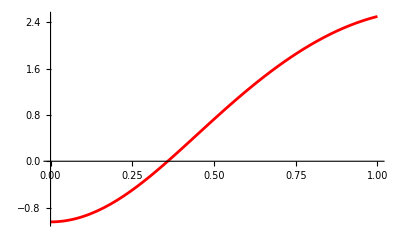

```mathematica
plotψex=Plot[Evaluate[ψ[s]/. sol],{s,smin,smax},PlotRange->All, PlotStyle->Red]
```

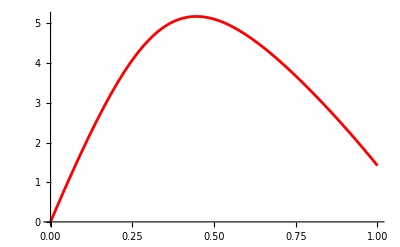

```mathematica
plotψpex=Plot[Evaluate[ψ'[s]/. sol],{s,smin,smax},PlotRange->All, PlotStyle->Red]
```

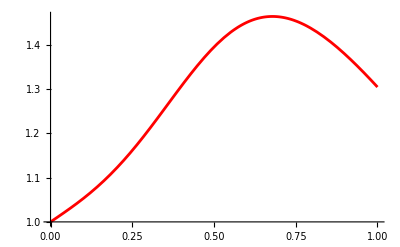

```mathematica
plotρex=Plot[Evaluate[ρ[s]/. sol],{s,smin,smax},PlotRange->All, PlotStyle->Red]
```

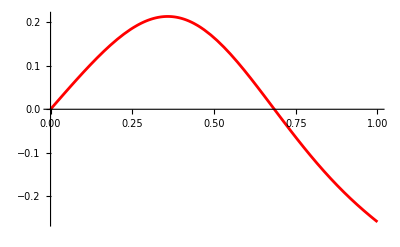

```mathematica
plotζex=Plot[Evaluate[ζ[s]/. sol],{s,smin,smax},PlotRange->All, PlotStyle->Red]
```

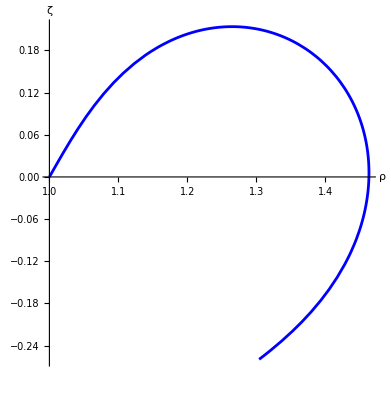

```mathematica
ParametricPlot[{ρ[s], ζ[s]}/.sol, {s, smin, smax},PlotStyle->Blue,AxesLabel->{"ρ","ζ"}]
```